# Numerisk integrering

## Exempel från föreläsningen

### Exempel 1 (Trapetsformeln)

Remove::rmnsm: There are no symbols matching "Global`*".

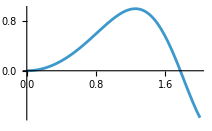

0.804428

0.804776

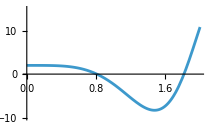

0.00288041

```mathematica
Remove["Global`*"]
f[x_]=Sin[x^2];
{a,b}={0,2};
Plot[f[x],{x,a,b}]
n=50;
h=(b-a)/n;
s=f[a];
For[i=1,i<n,++i,
xi=a+h*i;
s=s+2*f[xi];
]
s=s+f[b];
N[h*s/2]
(* Kontroll med Mathematica *)
NIntegrate[f[x],{x,0,2}]
(* Feluppskattning *)
d2f=FullSimplify[D[f[x],{x,2}]];
max=NMaxValue[{Abs[d2f],a≤x≤b},x];
Plot[d2f,{x,a,b},PlotRange->{-10,15}]
Abs[N[(b-a)^3/(12*n^2)]*max]
```

### Exempel 3 (Simpsons formel)

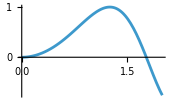

0.804777

0.804776

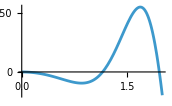

4.69162×10^-6

```mathematica
Remove["Global`*"]
f[x_]=Sin[x^2];
{a,b}={0,2};
Plot[f[x],{x,a,b}]
n=50;
h=(b-a)/n;
s=f[a];
For[i=1,i<n,i=i+1,
xi=a+h*i;
fact=2*2^Mod[i,2] (* faktorn är 4 för udda i och 2 för jämna i *);
s=s+fact*f[xi];
]
s=s+f[b];
N[h*s/3]
(* Kontroll med Mathematica *)
NIntegrate[f[x],{x,0,2}]
(* Feluppskattning *)
d4f=FullSimplify[D[f[x],{x,4}]];
max=NMaxValue[{Abs[d4f],a≤x≤b},x];
Plot[d4f,{x,a,b}]
Abs[N[(b-a)^5/(180*n^4)]*max ]
```

### Exempel 4 (Adaptiv integration med Trapetsformeln)

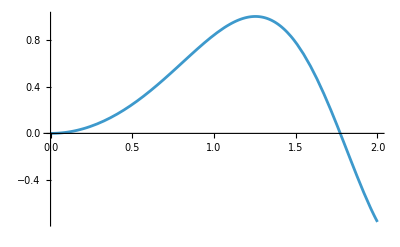

Felkrav: 0.0001

adaptivTrapets: 0.804776

Mathematicas NIntegrate: 0.8047764893437935

Absolut (relativt) fel: 4.3702×10^-7 (0.0000543033%)

```mathematica
Remove["Global`*"]
adaptivTrapets[f_,a_,b_,epsilon_]:=Module[{h,c,Th,T2h,epsh,lInt,rInt},
h=(b-a)/2;
c=(b+a)/2;
Th=(h/2)*(f[a]+2*f[c]+f[b]);
T2h=h*(f[a]+f[b]);
epsh=(Th-T2h)/3;
If[Abs[epsh]<epsilon,
Return[Th],
lInt=adaptivTrapets[f,a,c,epsilon/2];
rInt=adaptivTrapets[f,c,b,epsilon/2];
Return[lInt+rInt]
]
];
f[x_]=Sin[x^2];
{a,b}={0.,2.};
epsilon=10.^(-4); 
Print["Felkrav: ",epsilon];
Print["adaptivTrapets: ",ai=adaptivTrapets[f,a,b,epsilon]];
Print["Mathematicas NIntegrate: ",mi=NIntegrate[f[x],{x,a,b},WorkingPrecision->16]];
Print["Absolut (relativt) fel: ",Abs[ai-mi]," (",100*Abs[ai-mi]/ai,"%)"];
```

### Exempel 5 (Gaussisk kvadratur)

```mathematica
Remove["Global`*"]
{a,b}={0,2};
f[x_]=x^5-x;
n=3;
xi=NSolve[LegendreP[n,x]==0,x];
wi=2/(D[LegendreP[n,x],x]^2*(1-x^2))/.xi;
g=FullSimplify[(f[(a+b)/2+x*(b-a)/2]*(b-a)/2)]/.xi;
g.wi
NIntegrate[f[x],{x,a,b}]
```

8.66667

8.66667